```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g-g- t- t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT = { F[9],-F[9]} -> {V[4]};
allDiags = InsertFields[tops0,processGGT, InsertionLevel-> {Particles},GenericModel->"../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC",ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA_FC} initialized

classes model {../../Models/Top-FormFactors-FA/Top-FormFactors-FA} initialized

in total: 1 Particles insertion

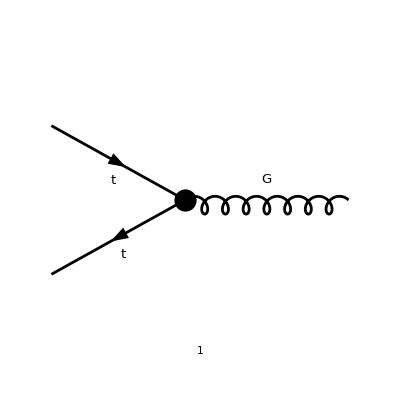

```mathematica
goodDiags=DiagramExtract[allDiags,{1}]; 
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 150,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p1,p2},LorentzIndexNames->{μ,ν},OutgoingMomenta->{-p3},LoopMomenta->{q},SUNIndexNames->{aa,bb,cc3},SUNFIndexNames->{c1,c2,a},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[DiracSimplify[FCReplaceMomenta[SUNSimplify[DiracSimplify[ampA]],{p3-> -p1-p2}]]]
```

in total: 1 Particles amplitude

ⅈ gs T_c2c1^cc3 (π^2 itri yDM^2 (γ^μ.(γ̄)^6 ((C1+C11+C12) (-p1·(p1+p2)-p2·(p1+p2)+p1^2+p2^2)+(C1+2 C12) (p1+p2)^2+2 C00ren)+(γ·p2).(γ̄)^6 ((C1+2 C11) p2^μ-(C1+2 C12) p1^μ)+(γ·p1).(γ̄)^6 ((C1+2 C11) p1^μ-(C1+2 C12) p2^μ)+2 deltaCTL γ^μ.(γ̄)^7)+γ^μ)

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampB/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

```mathematica
ampEsimp3=FullSimplify[DiracSimplify[ampEsimp/.{itri->1}]]
```

ⅈ gs T_c2c1^cc3 (π^2 yDM^2 (γ^μ.(γ̄)^6 (2 (C00ren+(C12-C11) (p1·p2)-deltaCTL)+p1^2 (C1+2 C12)+p2^2 (C1+2 C12))+(γ·p2).(γ̄)^6 ((C1+2 C11) p2^μ-(C1+2 C12) p1^μ)+(γ·p1).(γ̄)^6 ((C1+2 C11) p1^μ-(C1+2 C12) p2^μ))+γ^μ (2 π^2 deltaCTL yDM^2+1))

## UFO Result from FeynRules

```mathematica
FFV1="Gamma(3,2,1)";
FFV2="Gamma(3,2,-1)*ProjM(-1,1)";
FFV3="Gamma(3,2,-1)*ProjP(-1,1)";
FFV7="P(-1,1)*P(3,1)*Gamma(-1,2,-2)*ProjP(-2,1) + (P(-1,3)*P(3,1)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + P(-1,2)*P(3,2)*Gamma(-1,2,-2)*ProjP(-2,1) + (P(-1,3)*P(3,2)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + (P(-1,1)*P(3,3)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + (P(-1,2)*P(3,3)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + (P(-1,1)**2*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,2)**2*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,1)*P(-1,3)*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,2)*P(-1,3)*Gamma(3,2,-2)*ProjP(-2,1))/2. + P(-1,3)**2*Gamma(3,2,-2)*ProjP(-2,1)";
FFV8=
"P(-1,1)*P(3,1)*Gamma(-1,2,-2)*ProjP(-2,1) + (P(-1,3)*P(3,1)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + P(-1,2)*P(3,2)*Gamma(-1,2,-2)*ProjP(-2,1) + (P(-1,3)*P(3,2)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + (P(-1,1)*P(3,3)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + (P(-1,2)*P(3,3)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + (P(-1,3)*P(3,3)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + (P(-1,1)**2*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,2)**2*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,1)*P(-1,3)*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,2)*P(-1,3)*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,3)**2*Gamma(3,2,-2)*ProjP(-2,1))/2.";
FFV9="P(-1,1)*P(3,1)*Gamma(-1,2,-2)*ProjP(-2,1) + (P(-1,3)*P(3,1)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + P(-1,2)*P(3,2)*Gamma(-1,2,-2)*ProjP(-2,1) + (P(-1,3)*P(3,2)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + (P(-1,1)*P(3,3)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + (P(-1,2)*P(3,3)*Gamma(-1,2,-2)*ProjP(-2,1))/2. + P(-1,3)*P(3,3)*Gamma(-1,2,-2)*ProjP(-2,1) + (P(-1,1)**2*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,2)**2*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,1)*P(-1,3)*Gamma(3,2,-2)*ProjP(-2,1))/2. + (P(-1,2)*P(-1,3)*Gamma(3,2,-2)*ProjP(-2,1))/2.";
```

#### Functions to convert from UFO to FeynCalc

```mathematica
P[a_,b_]:=Which[a>0,FVD[ToExpression[StringJoin["p",ToString[b]]],a],a==-1,FVD[ToExpression[StringJoin["p",ToString[b]]],aa],a==-2,FVD[ToExpression[StringJoin["p",ToString[b]]],bb]]/.{3->μ,4->ν};
GAMMA[a_,b_,c_]:= Which[a==3,GAD[μ],a==4,GAD[ν],a==-1,GAD[aa],a==-2,GAD[bb]];
Metric[a_,b_]:=MTD[a,b]/.{3->μ,4->ν};
ProjP[a_,b_]:= 1;
ProjM[a_,b_]:=1;
Convert[expr_]:=(ToExpression[StringReplace[expr,{"Gamma"->"GAMMA","/4."->"/4","/2."->"/2","**2"-> "^2"}],TraditionalForm]/.{GAD[aa] FVD[a_,aa]:>  GSD[a],GAD[bb] FVD[a_,bb]:>  GSD[a],FVD[a_,aa]^2:> SPD[a,a],FVD[a_,aa] FVD[b_,aa]:>SPD[a,b]}).GA[6]
```

```mathematica
FFV1expr=DiracSimplify[Convert[FFV1]/.{GA[6]->1}]
FFV2expr=DiracSimplify[Convert[FFV2]/.{GA[6]->GA[7]}]
FFV3expr=DiracSimplify[Convert[FFV3]]
FFV7expr=DiracSimplify[Convert[FFV7]]
FFV8expr=DiracSimplify[Convert[FFV8]]
FFV9expr=DiracSimplify[Convert[FFV9]]
```

γ^μ

γ^μ.(γ̄)^7

γ^μ.(γ̄)^6

1/2 p1^2 γ^μ.(γ̄)^6+p1^μ (γ·p1).(γ̄)^6+1/2 γ^μ.(γ̄)^6 (p1·p3)+1/2 p1^μ (γ·p3).(γ̄)^6+1/2 p3^μ (γ·p1).(γ̄)^6+1/2 p2^2 γ^μ.(γ̄)^6+p2^μ (γ·p2).(γ̄)^6+1/2 γ^μ.(γ̄)^6 (p2·p3)+1/2 p2^μ (γ·p3).(γ̄)^6+1/2 p3^μ (γ·p2).(γ̄)^6+p3^2 γ^μ.(γ̄)^6

1/2 p1^2 γ^μ.(γ̄)^6+p1^μ (γ·p1).(γ̄)^6+1/2 γ^μ.(γ̄)^6 (p1·p3)+1/2 p1^μ (γ·p3).(γ̄)^6+1/2 p3^μ (γ·p1).(γ̄)^6+1/2 p2^2 γ^μ.(γ̄)^6+p2^μ (γ·p2).(γ̄)^6+1/2 γ^μ.(γ̄)^6 (p2·p3)+1/2 p2^μ (γ·p3).(γ̄)^6+1/2 p3^μ (γ·p2).(γ̄)^6+1/2 p3^2 γ^μ.(γ̄)^6+1/2 p3^μ (γ·p3).(γ̄)^6

1/2 p1^2 γ^μ.(γ̄)^6+p1^μ (γ·p1).(γ̄)^6+1/2 γ^μ.(γ̄)^6 (p1·p3)+1/2 p1^μ (γ·p3).(γ̄)^6+1/2 p3^μ (γ·p1).(γ̄)^6+1/2 p2^2 γ^μ.(γ̄)^6+p2^μ (γ·p2).(γ̄)^6+1/2 γ^μ.(γ̄)^6 (p2·p3)+1/2 p2^μ (γ·p3).(γ̄)^6+1/2 p3^μ (γ·p2).(γ̄)^6+p3^μ (γ·p3).(γ̄)^6

```mathematica
color={SUNTF[{SUNIndex[cc3]},SUNFIndex[c2],SUNFIndex[c1]]}
```

{T_c2c1^cc3}

```mathematica
GC12=I*gs;
GC68=2*deltaCTL*Pi^2*I*gs*yDM^2;
GC64=2*C00ren*Pi^2*I*gs*yDM^2;
GC67=2*C12*Pi^2*I*gs*yDM^2;
GC65=2*C1*Pi^2*I*gs*yDM^2;
GC66=2*C11*Pi^2*I*gs*yDM^2;
couplings={{GC12,GC68,GC64,GC67,GC65,GC66}};
LFFVV={FFV1expr,FFV2expr,FFV3expr,FFV7expr,FFV8expr,FFV9expr};
```

```mathematica
ttGG = Total[Table[couplings[[i,j]] color[[i]] LFFVV[[j]],{i,1,1},{j,1,6}],2];
```

```mathematica
ttGGsimp=Simplify[ttGG/.{DiracGamma[7]->1-DiracGamma[6]}];
ttGGsimp2=Simplify[FCReplaceMomenta[ttGGsimp,{p3->-p1-p2}]];
ttGGsimp3=FullSimplify[ExpandScalarProduct[DiracSimplify[ttGGsimp2]]];
```

```mathematica
Collect[ampEsimp3/(I Pi^2 gs yDM^2 color[[1]]),{C00ren,C1,C11,C12,deltaCTL},FullSimplify]
```

2 C00ren γ^μ.(γ̄)^6+C1 ((p1^2+p2^2) γ^μ.(γ̄)^6+(p1^μ-p2^μ) ((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6))+2 C11 (p1^μ (γ·p1).(γ̄)^6-γ^μ.(γ̄)^6 (p1·p2)+p2^μ (γ·p2).(γ̄)^6)+C12 (2 γ^μ.(γ̄)^6 (p1·p2+p1^2+p2^2)-2 p1^μ (γ·p2).(γ̄)^6-2 p2^μ (γ·p1).(γ̄)^6)+2 deltaCTL (γ^μ-γ^μ.(γ̄)^6)+γ^μ/(π^2 yDM^2)

```mathematica
Collect[ttGGsimp3/(I Pi^2 gs yDM^2 color[[1]]),{C00ren,C1,C11,C12,deltaCTL},FullSimplify]
```

2 C00ren γ^μ.(γ̄)^6+C1 ((p1^2+p2^2) γ^μ.(γ̄)^6+(p1^μ-p2^μ) ((γ·p1).(γ̄)^6-(γ·p2).(γ̄)^6))+2 C11 (p1^μ (γ·p1).(γ̄)^6-γ^μ.(γ̄)^6 (p1·p2)+p2^μ (γ·p2).(γ̄)^6)+C12 (2 γ^μ.(γ̄)^6 (p1·p2+p1^2+p2^2)-2 p1^μ (γ·p2).(γ̄)^6-2 p2^μ (γ·p1).(γ̄)^6)+2 deltaCTL (γ^μ-γ^μ.(γ̄)^6)+γ^μ/(π^2 yDM^2)

```mathematica
FullSimplify[%51-%50]
```

0